```mathematica
Nt = 100;
ti = 0; tf = 10; 
deltat = (tf - ti) /Nt ;
Nx = 100; 
xi = -2; xf = 8; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

1.

```mathematica
rs = Table[0.1*i,{i,1,30}];

maxevalsCN = Table[0,{i,1,Length[rs]}];
maxevalsEuler = Table[0,{i,1,Length[rs]}];
maxevalsRK2 = Table[0,{i,1,Length[rs]}];
maxevalsRK4 = Table[0,{i,1,Length[rs]}];
maxevalsN = Table[0,{i,1,Length[rs]}];
```

```mathematica
(-((π)^2 ) / (3h^2))- (1/6)//N
```

-8.5

```mathematica
Do[

deltat = deltax * rs[[p]];

h = (2*Pi)/ (Nx);

T = Array[#&,Nt,{ti,tf}]//N;

(*a = -2;
b = 8;*)

(*Equal X Spacing*)
(*X = Array[#&,Nx,{a,b}]//N*)

(*Equal X spacing that appears to be more accurate when transforming to [0,2pi]*)
(*X =  Table[xm = xi + m *deltax, {m, 0, Nx -1 }]//N*)

(*X spacing as defined in http://easymeca.mobile.basilisk.fr/sandbox/easystab/matlabdifmatsuite.pdf*)
X = Table[(i-1)*h,{i,1,Nx}]//N;

(*Transform X from [a,b] to [0,2pi]*)
(*X = ((X-a) * 2*Pi) / (b-a)*)

(************************************************************************************************************)

(*Derivative Matrix*)
D1 = Table[If[ k≠ j, 1/2(-1)^(k - j)Cot[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}]//N;
D2 = Table[If[ k≠ j, -1/2(-1)^(k - j)((Csc[((k - j) * h)/2])^2), (-((π)^2 ) / (3h^2))- (1/6)//N],{k,1,Nx},{j,1,Nx}]//N;
DL1 = -c * D1 * deltat;
DL2 = (-c)^2 * D2 * (deltat)^2;

f[x_] =ⅇ^(- 4(x-π)^2);

(*Print["Max Difference is"<>ToString[Max[Abs[D1.F - f'[X]]]]];*)

(************************************************************************************************************)

(*CN*)
I1 = IdentityMatrix[Length[D1]];
A = I1 - ((DL1 / 2));
B = I1 + ((DL1 / 2));
M = Inverse[A].B;

(*Euler*)
Ieuler = IdentityMatrix[Length[D1]];
euler = Ieuler + DL1;

(*RK2*)
IRK2 = IdentityMatrix[Length[D1]];
Mrk = (IRK2 + (DL1) + ((1/2)* DL2));

(*RK4*)
(*IRK4 = IdentityMatrix[Length[D1]];
MRK4 = IRK4 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4]));*)

(*New Method*)
IN = IdentityMatrix[Length[D1]];
AN = IN - ((DL1 / 2)) + (DL2/12);
BN = IN + ((DL1 / 2)) + (DL2/12);
MN = Inverse[AN].BN;

(************************************************************************************************************)

(*Eigenvalues*)

(*CN*)
evals = Abs[Eigenvalues[N[M]]];
maxevalsCN[[p]] = Max[evals];

(*Euler*)
evalsEuler = Abs[Eigenvalues[N[euler]]];
maxevalsEuler[[p]] = Max[evalsEuler];

(*RK2*)
evalsRK2 = Abs[Eigenvalues[N[Mrk]]];
maxevalsRK2[[p]] = Max[evalsRK2];

(*RK4*)
(*evalsRK4 = Abs[Eigenvalues[N[MRK4]]];
maxevalsRK4[[p]] = Max[evalsRK4];*)

(*New Method*)
evalsN = Abs[Eigenvalues[N[MN]]];
maxevalsN[[p]] = Max[evalsN];



,{p,1,Length[rs]}]
```

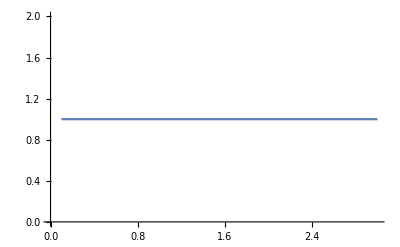

```mathematica
ListPlot[Transpose[{rs,maxevalsCN}], Joined->True]
```

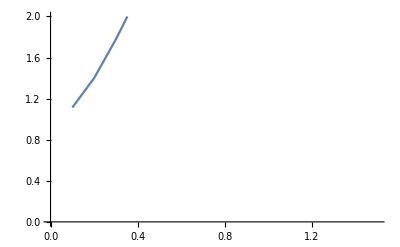

```mathematica
ListPlot[Transpose[{rs,maxevalsEuler}], Joined->True, PlotRange->{{0,1.5},{0,2}}]
```

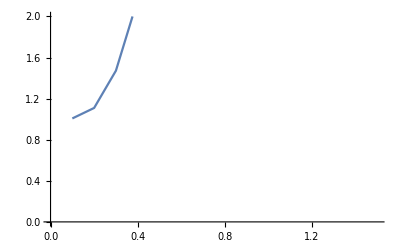

```mathematica
ListPlot[Transpose[{rs,maxevalsRK2}], Joined->True, PlotRange->{{0,1.5},{0,2}}]
```

```mathematica
maxevalsRK2
```

{1.00718,1.10932,1.4722,2.16552,3.16346,4.43598,5.96684,7.748,9.77533,12.0466,14.5604,17.3161,20.3131,23.551,27.125,31.,35.125,39.5,44.125,49.,54.125,59.5,65.125,71.,77.125,83.5,90.125,97.,104.125,111.5}

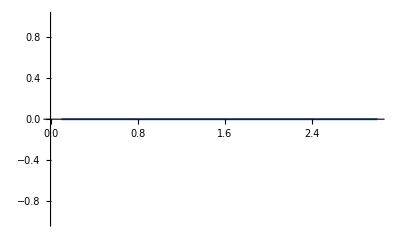

```mathematica
ListPlot[Transpose[{rs,maxevalsRK4}], Joined->True]
```

```mathematica
ListPlot[Transpose[{rs,maxevalsN}], Joined->True]
```

-Graphics-

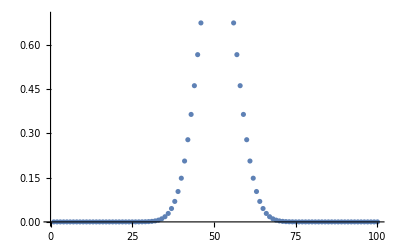

```mathematica
ListPlot[f[X]]
```